```mathematica
(*http://reference.wolfram.com/language/tutorial/SolvingLinearSystems.zh.html*)
LinearSolve[{{1,2},{4,5}},{3,6}]
```

{-1,2}

```mathematica
vectorGraphics[p_]:=Graphics[{Arrowheads[.07],Thickness[.01],Black,Arrow[{{0,0},p}]}]
```

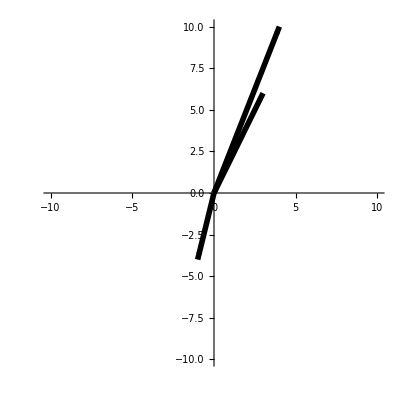

```mathematica
Show[vectorGraphics[{1,4} (-1)],vectorGraphics[{2,5} 2],vectorGraphics[{3,6}],PlotRange-> {{-10,10},{-10,10}},Axes-> True,AxesOrigin-> {0,0}]
```

```mathematica
RowReduce[{{1,2,3},{4,5,6}}]//MatrixForm
```

(1 | 0 | -1
0 | 1 | 2)

```mathematica
{lu,p,c}=LUDecomposition[{{1,2},{3,8}}]
l=lu SparseArray[{i_,j_}/;j<i->1,{2,2}]+IdentityMatrix[2];
l//MatrixForm
u=lu SparseArray[{i_,j_}/;j≥i->1,{2,2}];
u//MatrixForm
```

{{{1,2},{3,2}},{1,2},0}

(1 | 0
3 | 1)

(1 | 2
0 | 2)

```mathematica
{2, 1, 1} . {1, 1, 2} (* Inner product *)
```

5